## Para un n fija

## Definiciones

```mathematica
h=4.135667696*10^(-15); (*eV s*)
ℏ=6.582119569*10^(-16); (*eV s*)
c=3*^17 ;(*nm s^-1*)
Res=1*10^(-13);
```

```mathematica
ψn[n_,ρ_]:= ρ*SphericalBesselJ[n,ρ]
```

```mathematica
ξn[n_,ρ_]:=ρ*SphericalHankelH1[n,ρ]
```

```mathematica
dψn[n_,ρ_]:=-n *SphericalBesselJ[n,ρ]+ ρ * SphericalBesselJ[n-1,ρ] 
dξn[n_,ρ_]:=-n * SphericalHankelH1[n,ρ] + ρ* SphericalHankelH1[n-1,ρ]
```

nm : índice de refracción del medio
a : radio de la partícula
ω : frecuencia angular
ωp : frecuencia de plasma
γ : constante de amortiguamiento

nm = 1, A = a ωp/c , W= ω/ ωp, G= γ/ωp = 10^-2

```mathematica
nm=1;
G= 10*^-2;
```

```mathematica
mieSeccTrans[A_,W_,n_]:=Module[{np,m,x,an,bn,Qsca,Qext},
np=Sqrt[1-(1/(W(W+ I G)))];
m=np/nm;
x=W A nm;
an=((m ψn[n,m x] dψn[n,x])-(ψn[n,x] dψn[n,m x]))/((m ψn[n,m x] dξn[n,x])-(ξn[n,x] dψn[n,m x]));
bn=((ψn[n,m x] dψn[n,x])-(m ψn[n,x] dψn[n,m x]))/((ψn[n,m x] dξn[n,x])-(m ξn[n,x] dψn[n,m x]));
Qsca= (2 )/(W A)^2*((2 n +1)(Norm[an]^2+Norm[bn] ^2));
Qext =(2)/(W A)^2*((2 n +1)Re[an+ bn]);

{an,bn,Qsca,Qext}]
```

```mathematica
mieSeccTransAn[A_,W_,n_]:=Module[{np,m,x,an,Qsca,Qext},
np=Sqrt[1-(1/(W(W+ I G)))];
m=np/nm;
x=W A nm;
an=((m ψn[n,m x] dψn[n,x])-(ψn[n,x] dψn[n,m x]))/((m ψn[n,m x] dξn[n,x])-(ξn[n,x] dψn[n,m x]));
Qsca= (2 )/(W A)^2*((2 n +1)(Norm[an]^2));
Qext =(2)/(W A)^2*((2 n +1)Re[an]);

{an,Qsca,Qext}]
```

```mathematica
mieSeccTransBn[A_,W_,n_]:=Module[{np,m,x,bn,Qsca,Qext},
np=Sqrt[1-(1/(W(W+ I G)))];
m=np/nm;
x=W A nm;
bn=((ψn[n,m x] dψn[n,x])-(m ψn[n,x] dψn[n,m x]))/((ψn[n,m x] dξn[n,x])-(m ξn[n,x] dψn[n,m x]));
Qsca= (2 )/(W A)^2*((2 n +1)(Norm[bn] ^2));
Qext =(2)/(W A)^2*((2 n +1)Re[bn]);

{bn,Qsca,Qext}]
```

## Cálculos

### Modelo de Drude

```mathematica
(h c/500)/(13.142/ℏ)
```

1.2428×10^-16

```mathematica
mieSeccTransAn[60*(13.142/ℏ)/c,0.4,1][[3]]
```

2.07278

```mathematica
result1=Table[{(W*(13.142/ℏ)),mieSeccTransAn[60*(13.142/ℏ)/c,W,#][[3]]},{W,0.1,1,0.01}]&/@{1,2,3,4,5};
ListLinePlot[result1,AxesLabel->{"",""},PlotRange->All]
```

-Graphics-

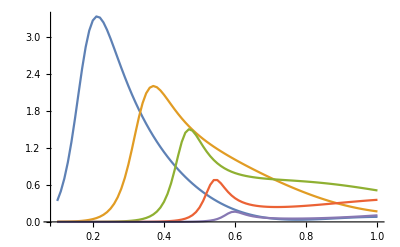

```mathematica
result2=Table[{W,mieSeccTransAn[5,W,#][[3]]},{W,0.1,1,0.01}]&/@{1,2,3,4,5};
ListLinePlot[result2,AxesLabel->{"",""},PlotRange->All]
```

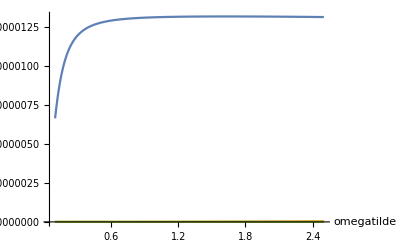

```mathematica
result3=Table[{W,mieSeccTransBn[0.1,W,#][[3]]},{W,0.1,2.5,0.01}]&/@{1,2,3};
ListLinePlot[result3,AxesLabel->{"omegatilde",""},PlotRange->All]
```

```mathematica
GoldenSearchMax[anc_,lower_,upper_,n_]:=Module[{a=N[lower],b=N[upper],c,d},k=0;
While[Abs[(b-(b-a)/GoldenRatio)-(a+(b-a)/GoldenRatio)]>Res,c=(b-(b-a)/GoldenRatio);
d=(a+(b-a)/GoldenRatio);
If[mieSeccTrans[anc,c,n][[4]]>mieSeccTrans[anc,d,n][[4]],(*Then*)b=d(*Else*); k=k+1;,a=c;k++;]];Return[(b+a)/2]];
```

```mathematica
ω1=Table[{anc,GoldenSearchMax[anc,0.1,1,1]},{anc,0.1,8,0.01}];
```

```mathematica
ω2=Table[{anc,GoldenSearchMax[anc,0.1,1,2]},{anc,0.1,8,0.01}];
```

```mathematica
ω3=Table[{anc,GoldenSearchMax[anc,0.1,1,3]},{anc,0.1,8,0.01}];
```

```mathematica
ω4=Table[{anc,GoldenSearchMax[anc,0.1,0.7,4]},{anc,0.1,8,0.01}];
```

```mathematica
ω5=Table[{anc,GoldenSearchMax[anc,0.1,0.7,5]},{anc,0.1,8,0.01}];
```

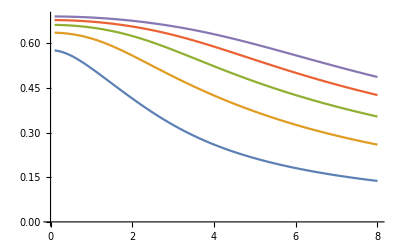

```mathematica
ListLinePlot[{ω1,ω2,ω3,ω4,ω5},PlotRange->All]
```

```mathematica
(*ResourceFunction["MaTeXInstall"][]
```

```mathematica
(*ConfigureMaTeX[
"pdfLaTeX"->"C:\\Users\\Lunita\\AppData\\Local\\Programs\\MiKTeX\\miktex\\bin\\x64\\pdflatex.exe","Ghostscript"->"C:\\Program Files\\gs\\gs10.03.1\\bin\\gswin64c.exe"
]
```

```mathematica
Needs["MaTeX`"]
```

```mathematica
MaTeX["x^2"]
```

-Graphics-

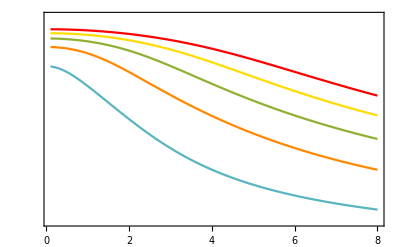

```mathematica
electricResonances=ListLinePlot[{Style[ω1,RGBColor[0.349,0.71,0.749]],Style[ω2,RGBColor[1,0.533,0]],Style[ω3],Style[ω4,RGBColor[1,0.863,0]],Style[ω5,Red]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],
FrameLabel->{{Style[MaTeX["\omega_l/ \omega_p"],Magnification->1.5],None},{Style[MaTeX["a\omega_p/c"],Magnification->1.5],None}},LabelStyle->{FontFamily->"CMU Serif",FontSize->20},FrameTicks->{{None,All},{Automatic,None}},PlotRange->{{0.1,8},{0.1,0.73}},PlotLegends->Placed[LineLegend[{Style[#,"CMU Serif",FontSize->20]&/@{MaTeX["l=1"],MaTeX["l=2"],MaTeX["l=3"],MaTeX["l=4"],MaTeX["l=5"]}},LegendMarkerSize->15,LegendMargins->-0.1,Spacings->0.05],{0.85,0.65}]]
```

```mathematica
a0=Table[{n,GoldenSearchMax[0.1,0.1,0.7,n]},{n,1,5,1}];
a1=Table[{n,GoldenSearchMax[1,0.1,0.7,n]},{n,1,5,1}];
a2=Table[{n,GoldenSearchMax[2,0.1,0.7,n]},{n,1,5,1}];
a3=Table[{n,GoldenSearchMax[3,0.1,0.7,n]},{n,1,5,1}];
a4=Table[{n,GoldenSearchMax[4,0.1,0.7,n]},{n,1,5,1}];
a5=Table[{n,GoldenSearchMax[5,0.1,0.7,n]},{n,1,5,1}];
a6=Table[{n,GoldenSearchMax[6,0.1,0.7,n]},{n,1,5,1}];
a7=Table[{n,GoldenSearchMax[7,0.1,0.7,n]},{n,1,5,1}];
a8=Table[{n,GoldenSearchMax[8,0.1,0.7,n]},{n,1,5,1}];
```

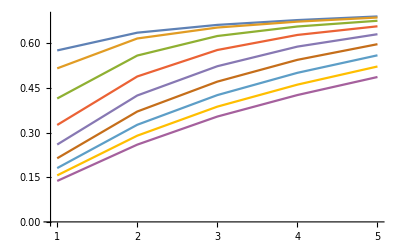

```mathematica
ListLinePlot[{a0,a1,a2,a3,a4,a5,a6,a7,a8}]
```

```mathematica
ωtilde1=Table[{n,GoldenSearchMax[1,0.1,0.7,n]},{n,1,5,1}]
```

{{1,0.516275},{2,0.616756},{3,0.653552},{4,0.673354},{5,0.687233}}

```mathematica
mieSeccTransBn[A_,W_,n_]:=Module[{np,m,x,bn,Qsca,Qext},
np=Sqrt[1-(1/(W(W+ I G)))];
m=np/nm;
x=W A nm;
bn=((ψn[n,m x] dψn[n,x])-(m ψn[n,x] dψn[n,m x]))/((ψn[n,m x] dξn[n,x])-(m ξn[n,x] dψn[n,m x]));
Qsca= (2 )/(W A)^2*((2 n +1)(Norm[bn] ^2));
Qext =(2)/(W A)^2*((2 n +1)Re[bn]);

{bn,Qsca,Qext}]
```

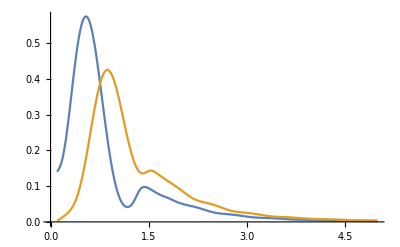

```mathematica
result3=Table[{W,mieSeccTransBn[5,W,#][[3]]},{W,0.1,5,0.01}]&/@{1,2};
ListLinePlot[result3,AxesLabel->{"",""},PlotRange->All]
```

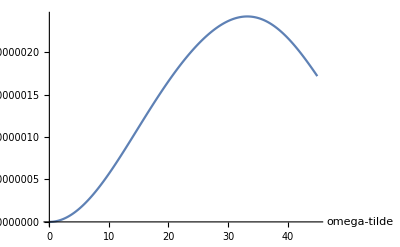

```mathematica
resultBn2=Table[{W,mieSeccTransBn[#,W,2][[3]]},{W,0.1,45,0.01}]&/@{0.1};
ListLinePlot[resultBn2,AxesLabel->{"omega-tilde",""},PlotRange->All]
```

```mathematica
resBn=10^{-9};
```

```mathematica
GoldenSearchMaxBn[anc_,lower_,upper_,n_]:=Module[{a=N[lower],b=N[upper],c,d},k=0;
While[Abs[(b-(b-a)/GoldenRatio)-(a+(b-a)/GoldenRatio)]>Res,c=(b-(b-a)/GoldenRatio);
d=(a+(b-a)/GoldenRatio);
If[mieSeccTransBn[anc,c,n][[3]]>mieSeccTransBn[anc,d,n][[3]],(*Then*)b=d(*Else*); k=k+1;,a=c;k++;]];Return[(b+a)/2]];
```

```mathematica
GoldenSearchMaxBn[4.98,0.1,1,1]
```

0.544471

```mathematica
ω1Bn=Table[{anc,GoldenSearchMaxBn[anc,0.1,5,1]},{anc,1,4.97,0.01}];
ω12Bn=Table[{anc,GoldenSearchMaxBn[anc,0.1,0.7,1]},{anc,4.98,8,0.01}];
```

```mathematica
ω2Bn=Table[{anc,GoldenSearchMaxBn[anc,0.1,5,2]},{anc,1,5,0.01}];
ω21Bn=Table[{anc,GoldenSearchMaxBn[anc,0.1,1,2]},{anc,5.01,8,0.01}];
```

```mathematica
ω3Bn=Table[{anc,GoldenSearchMaxBn[anc,0.1,5.5,3]},{anc,1,5.9,0.01}];
ω31Bn=Table[{anc,GoldenSearchMaxBn[anc,0.1,1,3]},{anc,5.91,8,0.01}];
```

```mathematica
ω4Bn=Table[{anc,GoldenSearchMaxBn[anc,0.05,9,4]},{anc,1,8,0.01}];
```

```mathematica
ω5Bn=Table[{anc,GoldenSearchMaxBn[anc,0.05,9,5]},{anc,0.4,8,0.01}];
```

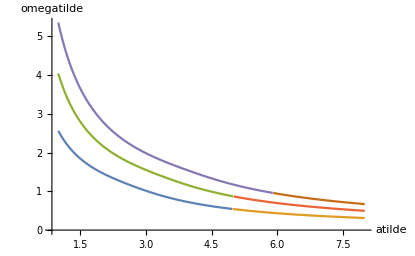

```mathematica
magneticResonances=ListLinePlot[{ω1Bn,ω12Bn,ω2Bn,ω21Bn,ω3Bn,ω31Bn},AxesLabel->{"atilde","omegatilde"},PlotRange->All]
```